-Graphics-

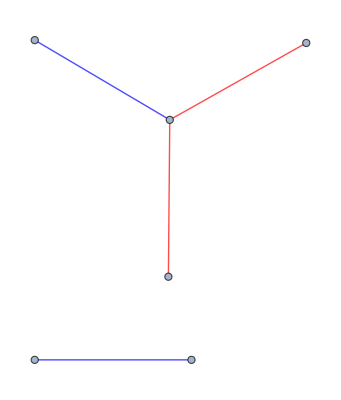

```mathematica
g=Graph[{a->b,a->c,c->a,b->a,a->y,u->v}]

Graph[SubsetReplace[EdgeList[g],{{x_->y_,y_->x_}:>Annotation[x<->y,EdgeStyle->{Red}],{x_->y_}:>Annotation[x<->y,EdgeStyle->{Blue}]}]]
```

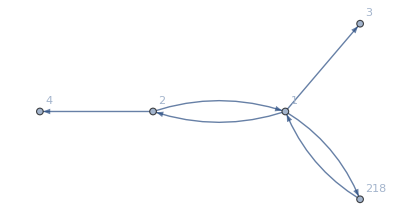

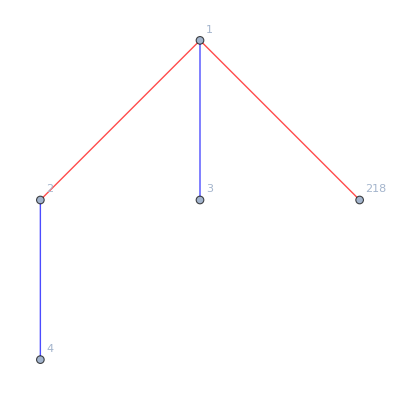

```mathematica
g=Graph[{1->2,1->3,1->218,2->1,2->4,218->1},VertexLabels->Automatic]
newEdges=Replace[GatherBy[EdgeList[g],Sort],{{DirectedEdge[a_,b_],DirectedEdge[b_,a_]}:>Style[UndirectedEdge[a,b],Red],{DirectedEdge[a_,b_]}:>Style[UndirectedEdge[a,b],Blue]},{1}];
Graph[newEdges,VertexLabels->Automatic]
```

```mathematica
x={1,2,1,3,1,218,2,1,2,4,218,1};
```

```mathematica
DeleteDuplicates[ReplacePart[x,Table[{{i},{i+1}}->DirectedEdge[x[[i]],x[[i+1]]],{i,1,Length@x,2}]]]
```

{1->2,1->3,1->218,2->1,2->4,218->1}

```mathematica
g0=Import["/home/justanotherlad/Documents/BTech Degree Project/twitter_combined.txt"];
```

```mathematica
g1=ToExpression[StringSplit[g0]]
```

{214328887,34428380,17116707,28465635,380580781,18996905,221036078,153460275,107830991,17868918,151338729,4841510,53811382,99841247,154263215,99841247,194403468,99841247,180165101,99841247,253509115,99841247,463410501}
 |  |  |  |

```mathematica
g2=DeleteDuplicates[ReplacePart[g1,Table[{{i},{i+1}}->DirectedEdge[g1[[i]],g1[[i+1]]],{i,1,Length@g1,2}]]]
```

{214328887->34428380,17116707->28465635,380580781->18996905,221036078->153460275,107830991->17868918,1768139,99841247->53811382,99841247->154263215,99841247->180165101,99841247->253509115,99841247->463410501}
 |  |  |  |

```mathematica
graph=Graph[g2]
```

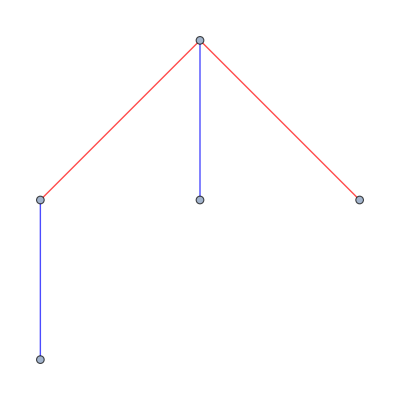

```mathematica
newgraph=Graph[SubsetReplace[EdgeList[graph],{{x_->y_,y_->x_}:>Annotation[x<->y,EdgeStyle->{Red}],{x_->y_}:>Annotation[x<->y,EdgeStyle->{Blue}]}]]
```

```mathematica
var=Subgraph[newgraph,{RandomInteger[{0,8000},19]},VertexLabels->Automatic]
```